```mathematica
(*user defined varibles*)
geomparams={l1->0.5,l2->0.4,b1->0.05,b2->0.05,g->9.81,m1->0.023,m2->0.025,m3->0.01};
actuation={θ1->π/4,θ2->π/6,d3->0.3};
(*Forward Kinematics*)
Ta={{1,0,0,a},{0,1,0,0},{0,0,1,0},{0,0,0,1}};
Tα={{1,0,0,0},{0, Cos[α],-Sin[α],0},{0,Sin[α],Cos[α],0},{0,0,0,1}};
Td={{1,0,0,0},{0,1,0,0},{0,0,1,d},{0,0,0,1}};
Tθ={{Cos[θ],-Sin[θ],0,0},{Sin[θ],Cos[θ],0,0},{0,0,1,0},{0,0,0,1}};
T=Td.Tθ.Ta.Tα;
DHTable={{l1,0,b1,θ1},{l2,0,b2,θ2},{0,0,d3,0}};
T1=T/.Inner[Rule,{a,α,d,θ},DHTable[[1]],List];
T2=T/.Inner[Rule,{a,α,d,θ},DHTable[[2]],List];
T3=T/.Inner[Rule,{a,α,d,θ},DHTable[[3]],List];
Teff=Simplify[T1.T2.T3];
TeffN=N[Teff/.geomparams/.actuation];
```

```mathematica
(*Inverse Kinematics*)
ikSCARA1[x_,y_,z_,θ1_,θ2_,d3_,Teff_,xval_,yval_,zval_]:=Module[{xpos,ypos,zpos,sold3,solθ12,expression,subs,new,root,theta1,theta2,θ1val,θ2val,t,d3val},
xpos=Teff[[1,4]]-x;
ypos=Teff[[2,4]]-y;
zpos=Teff[[3,4]]-z;
sold3=Solve[zpos==0,d3][[1]];
d3val=sold3/.geomparams/.{z->zval};
solθ12=Solve[{xpos,ypos}=={0,0},{Cos[θ1+θ2],Sin[θ1+θ2]}][[1]];
expression=Simplify[Numerator[Together[(Cos[θ1+θ2]^2+Sin[θ1+θ2]^2-1)/.solθ12]]];
subs={Cos[θ1]->(1-t^2)/(1+t^2),Sin[θ1]->2t/(1+t^2)};
new=Together[expression/.subs];
root=Solve[new==0,t];
theta1={θ1->2ArcTan[t/.root[[1]]],θ1->2ArcTan[t/.root[[2]]]};
θ1val=theta1/.geomparams/.{x->xval,y->yval};
theta2=ArcTan[Cos[θ1+θ2]/.solθ12,Sin[θ1+θ2]/.solθ12]-θ1;
θ2val={θ2->theta2/.theta1[[1]],θ2->theta2/.theta1[[2]]}/.geomparams/.{x->xval,y->yval};
Return[{Flatten[{θ1val[[1]],θ2val[[1]],d3val}],Flatten[{θ1val[[2]],θ2val[[2]],d3val}]}];];
ik1=ikSCARA1[x,y,z,θ1,θ2,d3,Teff,0.5,0.2,0.4]
```

{{θ1→-0.406961,θ2→1.87549,d3→0.3},{θ1→1.16797,θ2→-1.87549,d3→0.3}}

```mathematica
(*ikSCARA2[x_,y_,z_,θ1_,θ2_,d3_,Teff_,xval_,yval_,zval_,l1_,l2_,b1_,b2_]:=Module[{xpos,ypos,zpos,sold3,theta1,theta2,θ1val,θ2val,d3val},
xpos=Teff[[1,4]]-x;
ypos=Teff[[2,4]]-y;
zpos=Teff[[3,4]]-z;
d3val={d3->(-b1-b2+z)/.{z->zval}};
theta1={θ1->2 ArcTan[(4 l1 y-√(16 l1^2 y^2-4 (l1^2-l2^2-2 l1 x+x^2+y^2) (l1^2-l2^2+2 l1 x+x^2+y^2)))/(2 (l1^2-l2^2+2 l1 x+x^2+y^2))],θ1->2 ArcTan[(4 l1 y+√(16 l1^2 y^2-4 (l1^2-l2^2-2 l1 x+x^2+y^2) (l1^2-l2^2+2 l1 x+x^2+y^2)))/(2 (l1^2-l2^2+2 l1 x+x^2+y^2))]};
θ1val=theta1/.{x->xval,y->yval};
θ2val={θ2->(-θ1+ArcTan[(x-l1 Cos[θ1])/l2,(y-l1 Sin[θ1])/l2])/.{x->xval,y->yval}/.θ1val[[1]],θ2->(-θ1+ArcTan[(x-l1 Cos[θ1])/l2,(y-l1 Sin[θ1])/l2])/.{x->xval,y->yval}/.θ1val[[2]]};
Return[{Flatten[{θ1val[[1]],θ2val[[1]],d3val}],Flatten[{θ1val[[2]],θ2val[[2]],d3val}]}];];
ik2=ikSCARA2[x,y,z,θ1,θ2,d3,Teff,0.5,0.2,0.4,0.5,0.4,0.05,0.05]*)
```

```mathematica
(*verification*)
xpos=l1 Cos[θ1]+l2 Cos[θ1+θ2];
ypos=l1 Sin[θ1]+l2 Sin[θ1+θ2];
xpos/.geomparams/.ik1[[1]]
ypos/.geomparams/.ik1[[2]]
```

0.5

0.2

```mathematica
(*Workspace Analysis*)
r=0.5;
x0=0.2;
y0=0.3;
z0=0.2;
pmplot=ParametricPlot3D[{x0+r Cos[t],y0+r Sin[t],z0},{t,0,2 Pi}];
cyl=Graphics3D[{{"[◼]", "Annulus3D"}}[{{x0,y0,0},{x0,y0,0.3}},{0.1,0.9}]]
Show[{pmplot,cyl}]
taskspacepoints=Table[{x0+r Cos[t],y0+r Sin[t],z0},{t,0,2 π,0.1}];
len=Length[taskspacepoints];
jointangs=Table[ikSCARA2[x,y,z,θ1,θ2,d3,Teff,taskspacepoints[[ii,1]],taskspacepoints[[ii,2]],taskspacepoints[[ii,3]],0.5,0.4,0.05,0.05],{ii,1,len}];
```

-Graphics3D-

-Graphics3D-

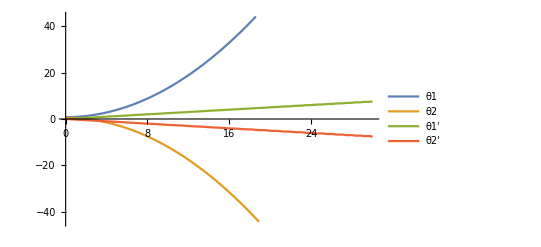

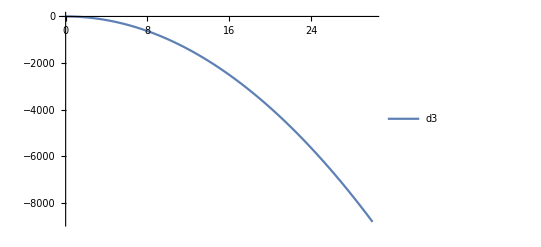

```mathematica
(*Forward Dynamics*)
subs={θ1->θ1[t],θ2->θ2[t],d3->d3[t]};
Dh1mid={l1/2,0,b1,θ1};
Dh2mid={l2/2,0,b2,θ2};
Dh3mid={0,0,d3/2,0};
T1mid=T/.Inner[Rule,{a,α,d,θ},Dh1mid,List];
T2mid=T/.Inner[Rule,{a,α,d,θ},Dh2mid,List];
T3mid=T/.Inner[Rule,{a,α,d,θ},Dh3mid,List];
T1midt=T1mid/.subs;
T2midt=Simplify[T1.T2mid/.subs];
T3midt=Simplify[T1.T2.T3mid/.subs];
cm1={T1midt[[1,4]],T1midt[[2,4]],T1midt[[3,4]]};
cm2=Simplify[{T2midt[[1,4]],T2midt[[2,4]],T2midt[[3,4]]}];
cm3=Simplify[{T3midt[[1,4]],T3midt[[2,4]],T3midt[[3,4]]}];
vcm1=D[cm1,t];
vcm2=D[cm2,t];
vcm3=D[cm3,t];
I1={{Ixx,0,0},{0,Iyy,0},{0,0,Izz}};
I2={{Ixx,0,0},{0,Iyy,0},{0,0,Izz}};
I3={{Ixx,0,0},{0,Iyy,0},{0,0,Izz}};
ke1trans = Simplify [m1/2(vcm1.vcm1)];
ke2trans = Simplify [Together[m2/2(vcm2.vcm2)]];
ke3trans = Simplify [Together[m3/2(vcm3.vcm3)]];
R1 = T1midt[[1;;3,1;;3]];
R2 = T2midt[[1;;3,1;;3]];
R3 = T3midt[[1;;3,1;;3]];
Ω1= Simplify[Transpose[R1].D[R1,t]];
Ω2= Simplify[Transpose[R2].D[R2,t]];
Ω3= Simplify[Transpose[R3].D[R3,t]];
ω1={Ω1[[3,2]],Ω1[[1,3]],Ω1[[2,1]]};
ω2={Ω2[[3,2]],Ω2[[1,3]],Ω2[[2,1]]};
ω3={Ω3[[3,2]],Ω3[[1,3]],Ω3[[2,1]]};
ke1rot=Simplify[(1/2)(ω1.I1.Transpose[ω1])];
ke2rot=Simplify[(1/2)(ω2.I2.Transpose[ω2])];
ke3rot=Simplify[(1/2)(ω3.I3.Transpose[ω3])];
ke=ke1rot+ke1trans+ke2rot+ke2trans+ke3rot+ke3trans;
h1={T1midt[[1,4]],T1midt[[2,4]],T1midt[[3,4]]}[[3]];
h2=Simplify[{T2midt[[1,4]],T2midt[[2,4]],T2midt[[3,4]]}][[3]];
h3=Simplify[{T3midt[[1,4]],T3midt[[2,4]],T3midt[[3,4]]}][[3]];
pe=m1 g h1+m2 g h2+m3 g h3;
L=Simplify[ke-pe];
q={θ1[t],θ2[t],d3[t]};
dq=D[q,t];
eqdyn1=Simplify[D[D[L,dq[[1]]],t]-D[L,q[[1]]]]/.geomparams/.(Izz->2.803);
eqdyn2=Simplify[D[D[L,dq[[2]]],t]-D[L,q[[2]]]]/.geomparams/.(Izz->0.637);
eqdyn3=Simplify[D[D[L,dq[[3]]],t]-D[L,q[[3]]]]/.geomparams;
s=NDSolve[{{eqdyn1,eqdyn2,eqdyn3}=={Sin[π/4],0,0},θ1[0]==π/4,θ2[0]==π/6,d3[0]==0.3,θ1'[0]==0,θ2'[0]==0,d3'[0]==0},{θ1,θ2,d3,θ1',θ2',d3'},{t,0,30}];
Plot[Evaluate[{θ1[t],θ2[t],θ1'[t],θ2'[t]}/. s],{t,0,30},PlotStyle->Automatic,PlotLegends->{θ1,θ2,θ1',θ2'}]
Plot[Evaluate[{d3[t]}/. s],{t,0,30},PlotStyle->Automatic,PlotLegends->{d3}]
```

```mathematica
(* Mass, Coriolis and Gravity Matrices*)
m11={Coefficient[eqdyn1,θ1''[t]],Coefficient[eqdyn1,θ2''[t]],Coefficient[eqdyn1,d3''[t]]}
m22={Coefficient[eqdyn2,θ1''[t]],Coefficient[eqdyn2,θ2''[t]],Coefficient[eqdyn2,d3''[t]]}
m33={Coefficient[eqdyn3,θ1''[t]],Coefficient[eqdyn3,θ2''[t]],Coefficient[eqdyn3,d3''[t]]}
MM={m11,m22,m33}
```

{8.42179+0.009 Cos[θ2[t]],5.6086+0.0045 Cos[θ2[t]],0}

{1/4 (5.1064+0.018 Cos[θ2[t]]),1.2766,0}

{0,0,0.0025}

{{8.42179+0.009 Cos[θ2[t]],5.6086+0.0045 Cos[θ2[t]],0},{1/4 (5.1064+0.018 Cos[θ2[t]]),1.2766,0},{0,0,0.0025}}

```mathematica
temp=IdentityMatrix[3];
For[i=1,i≤3,i++,
For[j=1,j≤3,j++,
For[k=1,k≤3,k++,
temp[[i,j]]+=0.5*(D[MM[[i,j]],q[[k]]]+D[MM[[i,k]],q[[j]]]-D[MM[[k,j]],q[[i]]])*D[q[[k]],t];
];
];
]
Cor=Chop[temp];
Cor // MatrixForm
```

(1.-0.0045 Sin[θ2[t]] θ2'[t] | -0.0045 Sin[θ2[t]] θ1'[t]-0.0045 Sin[θ2[t]] θ2'[t] | 0
0.0045 Sin[θ2[t]] θ1'[t] | 1. | 0
0 | 0 | 1.)

```mathematica
G=D[(pe/.geomparams),{q}]
```

{0,0,0.04905}

```mathematica
θddotdes=Join[D[θdotdes,t],{0}];
MM.θddotdes+Cor.dq+G
```

{{{8.42179+0.009 Cos[θ2[t]],5.6086+0.0045 Cos[θ2[t]],0},{1/4 (5.1064+0.018 Cos[θ2[t]]),1.2766,0},{0,0,0.0025}}.Join[0,{0}]+θ1'[t] (1.-0.0045 Sin[θ2[t]] θ2'[t])+θ2'[t] (-0.0045 Sin[θ2[t]] θ1'[t]-0.0045 Sin[θ2[t]] θ2'[t]),{{8.42179+0.009 Cos[θ2[t]],5.6086+0.0045 Cos[θ2[t]],0},{1/4 (5.1064+0.018 Cos[θ2[t]]),1.2766,0},{0,0,0.0025}}.Join[0,{0}]+0.0045 Sin[θ2[t]] θ1'[t]^2+1. θ2'[t],0.04905+{{8.42179+0.009 Cos[θ2[t]],5.6086+0.0045 Cos[θ2[t]],0},{1/4 (5.1064+0.018 Cos[θ2[t]]),1.2766,0},{0,0,0.0025}}.Join[0,{0}]+1. d3'[t]}

```mathematica
(*Inverse Dynamics & Tragectory Planning*)
subsxy={x->x[t],y->y[t],z->z[t]};
th1exp=2 ArcTan[(4 l1 y-√(16 l1^2 y^2-4 (l1^2-l2^2-2 l1 x+x^2+y^2) (l1^2-l2^2+2 l1 x+x^2+y^2)))/(2 (l1^2-l2^2+2 l1 x+x^2+y^2))];
vth1=D[(th1exp/.subsxy),t];
vvth1=D[vth1,t];
th2exp=(-th1exp+ArcTan[(x-l1 Cos[th1exp])/l2,(y-l1 Sin[th1exp])/l2]);
vth2=D[(th2exp/.subsxy),t];
vvth2=D[vth2,t];
d3exp=-b1-b2+z;
vd3=D[(d3exp/.subsxy),t];
vvd3=D[vd3,t];
theta=a0+a1 t+a2 t^2+a3 t^3;
traj={x0+r Cos[theta],y0+r Sin[theta]};
theta0=(a0+a1 t+a2 t^2+a3 t^3)/.{t->0};
thetatf=((a0+a1 t+a2 t^2+a3 t^3)/.{t->tf})-2Pi;
dtheta=D[theta,t];
dtheta0=dtheta/.{t->0};
dthetatf=dtheta/.{t->tf};
trajparam=Solve[{theta0,thetatf,dtheta0,dthetatf}==0,{a0,a1,a2,a3}][[1]]
TF=10;
trajval=traj/.trajparam/.{tf->TF}
```

{a0→0,a1→0,a2→(6 π)/tf^2,a3→-(4 π)/tf^3}

{0.2+0.5 Cos[(3 π t^2)/50-(π t^3)/250],0.3+0.5 Sin[(3 π t^2)/50-(π t^3)/250]}

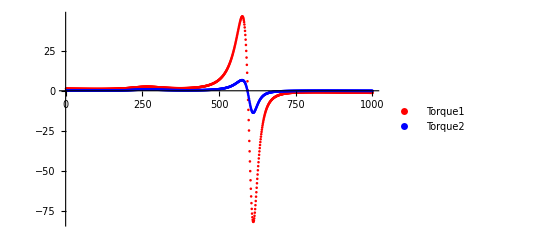

```mathematica
xtraj=trajval[[1]];
dxtraj=D[xtraj,t];
ddxtraj=D[dxtraj,t];
ytraj=trajval[[2]];
dytraj=D[ytraj,t];
ddytraj=D[dytraj,t];
iktrj=ikSCARA1[x,y,z,θ1,θ2,d3,Teff,trajval[[1]],trajval[[2]],0.4][[1]];
iktrjt=iktrj/.{θ1->θ1[t],θ2->θ2[t]};
Table[iktrj/.{t->ii},{ii,0,TF,0.1}];
theta1dot=vth1/.geomparams/.{x[t]->xtraj,y[t]->ytraj,x'[t]->dxtraj,y'[t]->dytraj};
theta2dot=vth2/.geomparams/.{x[t]->xtraj,y[t]->ytraj,x'[t]->dxtraj,y'[t]->dytraj};
theta1ddot=vvth1/.geomparams/.{x[t]->xtraj,y[t]->ytraj,x'[t]->dxtraj,y'[t]->dytraj,x''[t]->ddxtraj,y''[t]->ddytraj};
theta2ddot=vvth2/.geomparams/.{x[t]->xtraj,y[t]->ytraj,x'[t]->dxtraj,y'[t]->dytraj,x''[t]->ddxtraj,y''[t]->ddytraj};
tauinv1=eqdyn1/.iktrjt/.{θ1'[t]->theta1dot,θ1''[t]->theta1ddot,θ2'[t]->theta2dot,θ2''[t]->theta2ddot};
tauinv2=eqdyn2/.iktrjt/.{θ1'[t]->theta1dot,θ1''[t]->theta1ddot,θ2'[t]->theta2dot,θ2''[t]->theta2ddot};
tauinva=Table[tauinv1/.{t->ii},{ii,0,TF,0.01}];
tauinvb=Table[tauinv2/.{t->ii},{ii,0,TF,0.01}];
Show[ListPlot[tauinva,PlotRange->All,PlotStyle->Red,PlotLegends->{Torque1}],ListPlot[tauinvb,PlotRange->All,PlotStyle->Blue,PlotLegends->{Torque2}]]
```

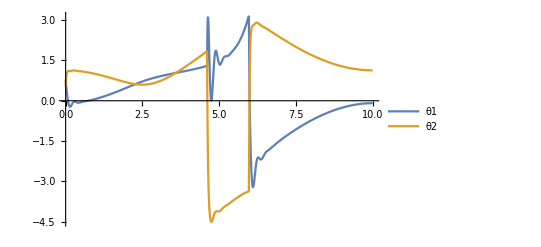

```mathematica
(*PD Control & Validation*)
Kp=5000*IdentityMatrix[2];
Kv=2*Sqrt[Kp]*IdentityMatrix[2];
θdes={θ1,θ2}/.iktrj;
err=θdes-{θ1[t],θ2[t]};
θdotdes=D[θdes,t];
errdot=θdotdes-{θ1'[t],θ2'[t]};
τc=Kp.err+Kv.errdot;
s1=NDSolve[{{eqdyn1,eqdyn2}==τc,θ1[0]==π/4,θ2[0]==π/6,θ1'[0]==0,θ2'[0]==0},{θ1,θ2},{t,0,TF},Method->{"EquationSimplification"->"Residual"}];
Plot[Evaluate[{θ1[t],θ2[t]}/. s1],{t,0,TF},PlotStyle->Automatic,PlotLegends->{θ1,θ2}]
solList=Inner[Rule,Flatten[{θ1,θ2,time}],#,List]&/@Table[Flatten[{θ1[t],θ2[t],t}/. s1[[1]]],{t,0,TF,0.01}];
descir=Table[trajval/.{t->ii},{ii,0,TF,0.01}];
cirpoints={xpos,ypos}/.solList/.geomparams;
```

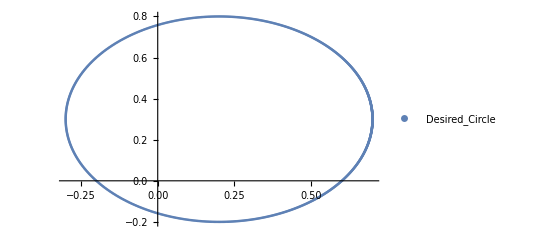

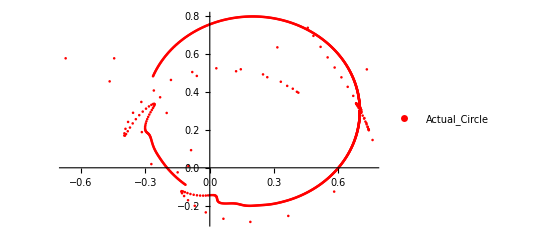

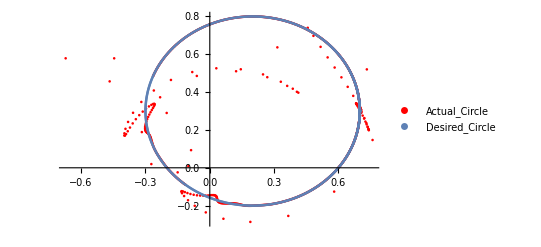

```mathematica
plot2=ListPlot[descir,PlotStyle->Automatic,PlotLegends->{Desired_Circle}]
plot1=ListPlot[cirpoints,PlotStyle->Red,PlotLegends->{Actual_Circle}]
Show[plot1,plot2]
```

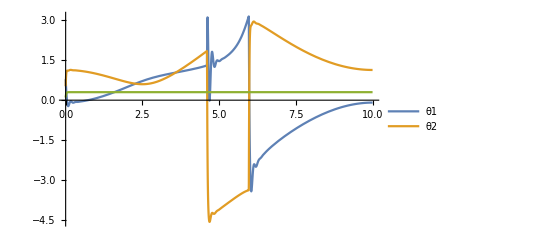

```mathematica
(*Computed Torque Control*)
Kp1=15000*IdentityMatrix[3];
Kv1=2*Sqrt[Kp1]*IdentityMatrix[3];
θdes1={θ1,θ2,0.3}/.iktrj;
err1=θdes1-{θ1[t],θ2[t],d3[t]};
θdotdes1=D[θdes1,t];
θddotdes1 =D[θdotdes1,t];
errdot1=θdotdes1-{θ1'[t],θ2'[t],d3'[t]};
τctau=MM.θddotdes1+Cor.dq+G+Kp1.err1+Kv1.errdot1;
τc=Kp.err+Kv.errdot;
s2=NDSolve[{{eqdyn1,eqdyn2,eqdyn3}==τctau,θ1[0]==π/4,θ2[0]==π/6,d3[0]==0.1,θ1'[0]==0,θ2'[0]==0,d3'[0]==0},{θ1,θ2,d3},{t,0,TF},Method->{"EquationSimplification"->"Residual"}];
Plot[Evaluate[{θ1[t],θ2[t],d3[t]}/. s2],{t,0,TF},PlotStyle->Automatic,PlotLegends->{θ1,θ2},PlotRange->All]
```

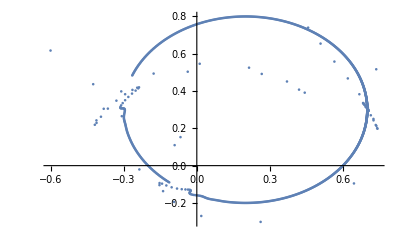

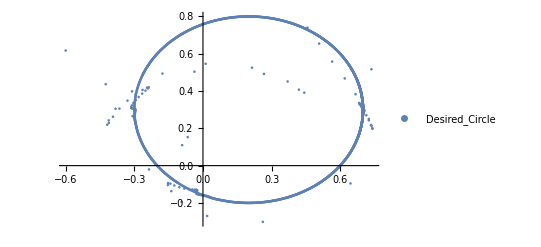

```mathematica
solList1=Inner[Rule,Flatten[{θ1,θ2,d3,time}],#,List]&/@Table[Flatten[{θ1[t],θ2[t],d3[t],t}/. s2[[1]]],{t,0,TF,0.01}];
cirpoints1={xpos,ypos}/.solList1/.geomparams;
plot11=ListPlot[cirpoints1]
Show[plot11,plot2]
```

```mathematica
(*LQR Control*)
eqdyn1a=eqdyn1/.{Izz->Iz1};
eqdyn2a=eqdyn2/.{Izz->Iz2};
	solacc=Simplify[Solve[{eqdyn1a,eqdyn2a}==0,{θ1''[t],θ2''[t]}]][[1]];
	subslist={θ1[t]->x1,θ2[t]->x2,θ1'[t]->x3,θ2'[t]->x4};
	f3exp=Together[(θ1''[t]/.solacc)/.subslist]
	f4exp=Together[(θ2''[t]/.solacc)/.subslist]
```

-(1. (1246.36 x3^2+567.378 x3 x4+283.689 x4^2+1. x3^2 Cos[x2]) Sin[x2])/(-177349.+962.667 Cos[x2]+1. Cos[x2]^2)

(1. (1871.51 x3^2+567.378 x3 x4+283.689 x4^2+2. x3^2 Cos[x2]+2. x3 x4 Cos[x2]+1. x4^2 Cos[x2]) Sin[x2])/(-177349.+962.667 Cos[x2]+1. Cos[x2]^2)

```mathematica
Jacob=Simplify[D[{x3,x4,f3exp,f4exp},{{x1,x2,x3,x4}}]]/.geomparams/.{Iz1->2.803,Iz2->0.637,x1->π/4,x2->π/6,x3->0.1,x4->0.1}
Eigenvalues[Jacob]
A=Jacob;
B={{0,0},{0,0},{1,0},{0,1}};
Q=IdentityMatrix[4];
R=IdentityMatrix[2];
```

{{0,0,1,0},{0,0,0,1},{0,0.000102771,0.0008673,0.000321434},{0,-0.000133507,-0.00122245,-0.000322415}}

{0.000309255+0.0115573 ⅈ,0.000309255-0.0115573 ⅈ,-0.0000736249+0. ⅈ,0.+0. ⅈ}

```mathematica
Psol=MatrixForm[RiccatiSolve[{A,B},{Q,R}]]
```

(1.73205 | 0.0000297361 | 1. | 0.000445617
0.0000297361 | 1.73197 | -0.000342846 | 0.999866
1. | -0.000342846 | 1.73292 | -0.000420627
0.000445617 | 0.999866 | -0.000420627 | 1.73165)

```mathematica
u=Inverse[R].Transpose[B].Psol.{x1,x2,x3,x4}
```

{{0,0,1,0},{0,0,0,1}}.(1.73205 | 0.0000297361 | 1. | 0.000445617
0.0000297361 | 1.73197 | -0.000342846 | 0.999866
1. | -0.000342846 | 1.73292 | -0.000420627
0.000445617 | 0.999866 | -0.000420627 | 1.73165).{x1,x2,x3,x4}